```mathematica
Name: Melissa Lee
Student ID: 105-128-234
Email: melissaloreleilee@gmail.com
Homework 5
```

For ϵ=0

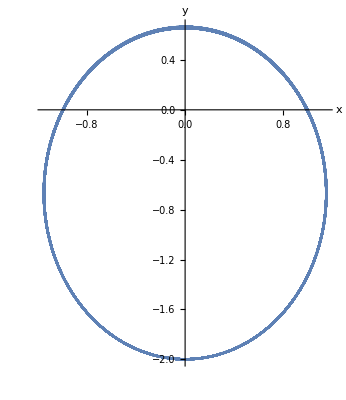

For ϵ=0.1

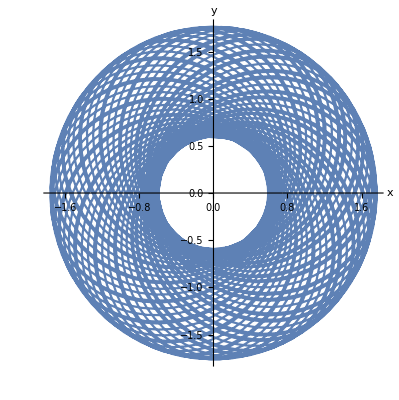

For ϵ=-0.4

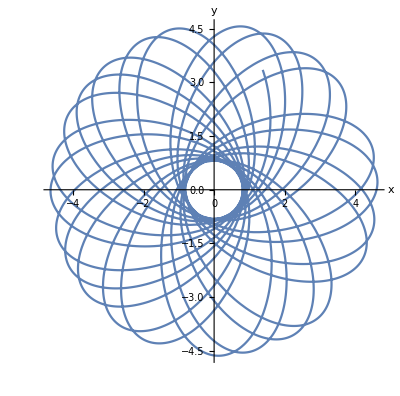

```mathematica
(*Problem 1*)
Remove["Global`*"]
SetAttributes[m,Constant];
(*Kinetic Energy*)
T =1/2 * m*(x'[t]^2+y'[t]^2);
(*Potential Energy*)
U=-4 π^2 m/((x[t]^2+y[t]^2)^(1/2))^(1+ϵ);
(*Lagrange*)
lag=T-U;
(*Euler-Lagrange*)
EL[q_]:= D[lag,q] - Dt[ D[lag,D[q,t]], t]==0//Simplify;
(*equation lists and initial conditions*)
ellist={EL[x[t]],EL[y[t]]};
iclist={x[0]==1,y[0]==0,x'[0]==-π,y'[0]==2π};
eqnlist=Join[ellist,iclist];
slist={x,y};
(*case 1: ϵ=0*)
Print["For ϵ=0"]
m=1;
ϵ=0;
soln= NDSolve[eqnlist,slist,{t,0,100},MaxSteps-> Infinity][[1]];
ParametricPlot[{x[t],y[t]}/.soln,{t,0,100},AxesLabel->{x,y},AspectRatio->Automatic,PlotRange->All]
(*case 2: ϵ=0.1*)
Print["For ϵ=0.1"]
ϵ=0.1;
soln= NDSolve[eqnlist,slist,{t,0,100},MaxSteps-> Infinity][[1]];
ParametricPlot[{x[t],y[t]}/.soln,{t,0,100},AxesLabel->{x,y},AspectRatio->Automatic,PlotRange->All]
(*case 3: ϵ=-0.4*)
Print["For ϵ=-0.4"]
ϵ=-0.4;
soln= NDSolve[eqnlist,slist,{t,0,100},MaxSteps-> Infinity][[1]];
ParametricPlot[{x[t],y[t]}/.soln,{t,0,100},AxesLabel->{x,y},AspectRatio->Automatic,PlotRange->All]
```

```mathematica
(*Problem 2*)
Remove["Global`*"]//Quiet
SetAttributes[m,Constant];
(*Kinetic Energy*)
T =1/2 * m*(x'[t]^2+y'[t]^2);
(*Potential Energy*)
U=-4 π^2 m/((x[t]^2+y[t]^2)^(1/2))^(1+ϵ);
(*Lagrange*)
lag=T-U;
(*Euler-Lagrange*)
EL[q_]:= D[lag,q] - Dt[ D[lag,D[q,t]], t]==0//Simplify;
(*equation lists and initial conditions*)
ellist={EL[x[t]],EL[y[t]]};
iclist={x[0]==1,y[0]==0,x'[0]==-π,y'[0]==2π};
eqnlist=Join[ellist,iclist];
slist={x,y};
(*case 1: ϵ=0*)
Print["For ϵ=0"]
(*variables*)
m=1;
ϵ=0;
soln= NDSolve[eqnlist,slist,{t,0,100},MaxSteps-> Infinity][[1]];
range={{-2,2},{-2,2}};
(*solve and then graph*)
sun[t_]=Graphics[{Yellow,Ball[{0,0},0.5]}];
earth[t_]:= Graphics[{Blue,Ball[{x[t],y[t]}/.soln,0.2]}];
sweep[t_]:=ListLinePlot[{{0,0},{x[t],y[t]}/.soln}];
traj[t_]:=ParametricPlot[{x[t1],y[t1]}/.soln,{t1,Max[t-10.,0],t},PlotStyle->Black];
pix[t_]:=Show[sun[t],earth[t],sweep[t],traj[t],Axes->True,PlotRange->range];
Animate[pix[t],{t,0,100}]
```

For ϵ=0

```mathematica
Remove["Global`*"]//Quiet
SetAttributes[m,Constant];
(*Kinetic Energy*)
T =1/2 * m*(x'[t]^2+y'[t]^2);
(*Potential Energy*)
U=-4 π^2 m/((x[t]^2+y[t]^2)^(1/2))^(1+ϵ);
(*Lagrange*)
lag=T-U;
(*Euler-Lagrange*)
EL[q_]:= D[lag,q] - Dt[ D[lag,D[q,t]], t]==0//Simplify;
(*equation lists and initial conditions*)
ellist={EL[x[t]],EL[y[t]]};
iclist={x[0]==1,y[0]==0,x'[0]==-π,y'[0]==2π};
eqnlist=Join[ellist,iclist];
slist={x,y};
(*case 2: ϵ=0.1*)
Print["For ϵ=0.1"]
(*variables*)
m=1;
ϵ=0.1;
soln= NDSolve[eqnlist,slist,{t,0,100},MaxSteps-> Infinity][[1]];
range={{-2,2},{-2,2}};
(*solve and then graph*)
sun[t_]=Graphics[{Yellow,Ball[{0,0},0.5]}];
earth[t_]:= Graphics[{Blue,Ball[{x[t],y[t]}/.soln,0.2]}];
sweep[t_]:=ListLinePlot[{{0,0},{x[t],y[t]}/.soln}];
traj[t_]:=ParametricPlot[{x[t1],y[t1]}/.soln,{t1,Max[t-10.,0],t},PlotStyle->Black];
pix[t_]:=Show[sun[t],earth[t],sweep[t],traj[t],Axes->True,PlotRange->range];
Animate[pix[t],{t,0,100}]
```

For ϵ=0.1

```mathematica
Remove["Global`*"]//Quiet
SetAttributes[m,Constant];
(*Kinetic Energy*)
T =1/2 * m*(x'[t]^2+y'[t]^2);
(*Potential Energy*)
U=-4 π^2 m/((x[t]^2+y[t]^2)^(1/2))^(1+ϵ);
(*Lagrange*)
lag=T-U;
(*Euler-Lagrange*)
EL[q_]:= D[lag,q] - Dt[ D[lag,D[q,t]], t]==0//Simplify;
(*equation lists and initial conditions*)
ellist={EL[x[t]],EL[y[t]]};
iclist={x[0]==1,y[0]==0,x'[0]==-π,y'[0]==2π};
eqnlist=Join[ellist,iclist];
slist={x,y};
(*case 3: ϵ=-0.4*)
Print["For ϵ=-0.4"]
(*variables*)
m=1;
ϵ=-0.4;
soln= NDSolve[eqnlist,slist,{t,0,100},MaxSteps-> Infinity][[1]];
range={{-5,5},{-5,5}};
(*solve and then graph*)
sun[t_]=Graphics[{Yellow,Ball[{0,0},0.5]}];
earth[t_]:= Graphics[{Blue,Ball[{x[t],y[t]}/.soln,0.2]}];
sweep[t_]:=ListLinePlot[{{0,0},{x[t],y[t]}/.soln}];
traj[t_]:=ParametricPlot[{x[t1],y[t1]}/.soln,{t1,Max[t-10.,0],t},PlotStyle->Black];
pix[t_]:=Show[sun[t],earth[t],sweep[t],traj[t],Axes->True,PlotRange->range];
Animate[pix[t],{t,0,100}]
```

For ϵ=-0.4

```mathematica
(*Problem 3*)
Remove["Global`*"]
(*Kinetic Energy*)
T =1/2 m1 (x1'[t]^2+y1'[t]^2)+1/2 m2 (x2'[t]^2+y2'[t]^2);
(*Potential Energy*)
U=-G m1 m2/(((x2[t]-x1[t])^2+(y2[t]-y1[t])^2)^(1/2))^(1+ϵ);
(*Lagrange*)
lag=T-U;
(*Euler-Lagrange*)
EL[q_]:= D[lag,q] - Dt[ D[lag,D[q,t]], t]==0//Simplify;
(*equation lists and initial conditions*)
ellist={EL[x1[t]],EL[y1[t]],EL[x2[t]],EL[y2[t]]};
iclist={x1[0]==0,y1[0]==10,x2[0]==0,y2[0]==0,x1'[0]==π/3,y1'[0]==0,x2'[0]==0,y2'[0]==0};
eqnlist=Join[ellist,iclist];
slist={x1,x2,y1,y2};
(*ϵ=0*)
Print["For ϵ=0"]
(*variables*)
G=1;
m1=10;
m2=15;
ϵ=0.1;
soln= NDSolve[eqnlist,slist,{t,0,100},MaxSteps-> Infinity][[1]];
range={{-5,50},{-10,10}};
(*solve and then graph*)
mass1[t_]:= Graphics[{PointSize[0.03],Point[{x1[t],y1[t]}/.soln]}]
mass2[t_]:= Graphics[{PointSize[0.03],Red,Point[{x2[t],y2[t]}/.soln]}]
cm[t_]:=Graphics[{PointSize[0.03],Blue,Point[{(m1 x1[t]+m2 x2[t])/(m1+m2),(m1 y1[t]+m2 y2[t])/(m1+m2)}/.soln]}];
cmPath[t_]:=ListLinePlot[{{(m1 x1[0]+m2 x2[0])/(m1+m2),(m1 y1[0]+m2 y2[0])/(m1+m2)}/.soln,{(m1 x1[t]+m2 x2[t])/(m1+m2),(m1 y1[t]+m2 y2[t])/(m1+m2)}/.soln}];
traj1[t_]:=ParametricPlot[{x1[t1],y1[t1]}/.soln,{t1,Max[t-10.,0],t},PlotStyle->Black];
traj2[t_]:=ParametricPlot[{x2[t1],y2[t1]}/.soln,{t1,Max[t-10.,0],t},PlotStyle->Red];
pix[t_]:=Show[mass1[t],mass2[t],cm[t],cmPath[t],traj1[t],traj2[t],Axes->True,PlotRange->range];
Animate[pix[t],{t,0,100}]
```

For ϵ=0